```mathematica
$HistoryLength=0;
Needs["VectorAnalysis`"]
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Clear[Eq0,EvapThickFilm,h,Bo,ϵ,K1,δ,Bi,m,r]
Eq0[h_,{Bo_,ϵ_,K1_,δ_,Bi_,m_,r_}]:=D[h, t]+Div[-h^3 Bo Grad[h]+h^3 Grad[Laplacian[h]]+(δ h^3)/(Bi h+K1)^3 Grad[h]+m(h/(K1+Bi h))^2 Grad[h]]+ϵ/(Bi h+K1) + (r)D[D[(h^2/(K1+Bi h)),x] h^3,x] ==0;
SetCoordinates[Cartesian[x,y,z]];
EvapThickFilm[Bo_,ϵ_,K1_,δ_,Bi_,m_,r_]:=Eq0[h[x,y,t],{Bo,ϵ,K1,δ,Bi,m,r}];
TraditionalForm[EvapThickFilm[Bo,ϵ,K1,δ,Bi,m,r]];
```

```mathematica
L = 54.773; 
TMax = 100; 
Off[NDSolve::mxsst]; 
hSol[x_?NumericQ,y_?NumericQ,t_?NumericQ] = h[x, y, t] /. 
   NDSolve[{EvapThickFilm[0.000, 0.0086, 1, 0, 1, 0*0.025, 0], 
      h[0, y, t] == h[L, y, t], h[x, 0, t] == h[x, L, t], 
      h[x, y, 0] == 1 + (-0.25*Cos[2*Pi*(x/L)] - 0.25*Sin[2*Pi*(x/L)])*
         Cos[2*Pi*(y/L)]}, h, {x, 0, L}, {y, 0, L}, {t, 0, TMax}, 
     MaxStepFraction -> 1/50][[1]]
```

InterpolatingFunction[{{0.,54.773},{0.,54.773},{0.,100.}},<>][x,y,t]

```mathematica
Plot[
NIntegrate[hSol[x, y, fac*TMax], {x, 0, L}, {y, 0, L}]*(0.14 * 10)/(2.35*10^-3*1400*10^3),
{fac,0,1}
]
(*NIntegrate[hSol[x, y, 0.2*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.3*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.4*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.5*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.6*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.7*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.8*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.82*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.85*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.87*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.90*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.95*TMax], {x, 0, L}, {y, 0, L}]
NIntegrate[hSol[x, y, 0.999*TMax], {x, 0, L}, {y, 0, L}]*)
```

$Aborted

```mathematica
Plot3D[
hSol[x, y, TMax], {x, 0, L}, {y, 0, L},
PlotPoints->25

]
```

-Graphics3D-

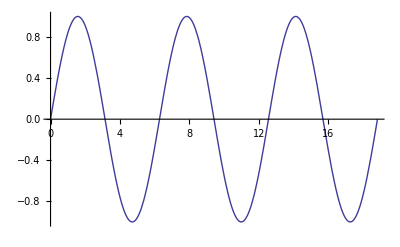
{0.007269,-Graphics-}

```mathematica
AbsoluteTiming[Plot[Sin[x],{x,0,6Pi},PerformanceGoal->Quality]]
```